# Correlation as Information

https://twitter.com/nntaleb/status/1135116646442590208/photo/1

```mathematica
ϕ[ρ_,K_]:=SurvivalFunction[BinormalDistribution[ρ],{K,K}]/SurvivalFunction[NormalDistribution[],K]//N
```

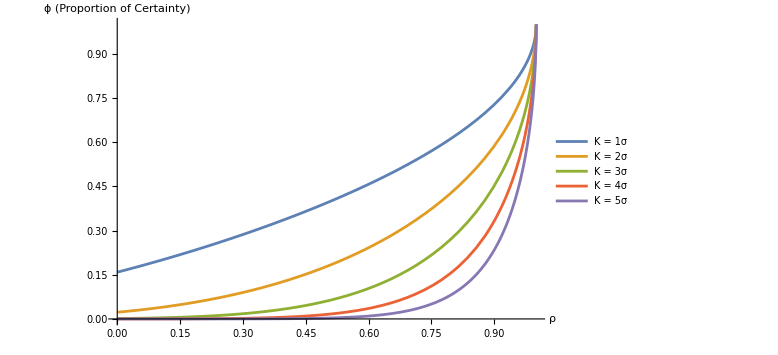

```mathematica
Plot[Evaluate[Table[ϕ[ρ,i],{i,1,5}]],{ρ,0,1},
AxesLabel->{ρ,"ϕ (Proportion of Certainty)"},
PlotLegends -> Placed[{"K = 1σ","K = 2σ","K = 3σ","K = 4σ","K = 5σ"},{Center,Top}],
ImageSize->Large]
```

Observe only after correlation more than 0.950 you only have 0.408 proportion of certainty for 5-sigma event.
Look at how IQ is normally distributed. N[Mean = 100, SD = 15]. Even at 0.98, proportion of certainty is 0.70. Now the problem, if IQ is not normally distributed, what happens?